# Exploring Food Data

Corwin Kerr

## What data is available?

The Wolfram Language has built-in knowledge base which powers WolframAlpha. I was curious about exploring the data associated with food, and ended up exploring smoothie colors.

Free form input can be used to start the search for available data.

```mathematica
strawberry=
```

And see what this is behind the scenes:

```mathematica
%//InputForm
```

Entity["Food", 
 {EntityProperty["Food", "FoodType"] -> 
   ContainsExactly[{Entity["FoodType", 
      "Strawberry"]}], 
  EntityProperty["Food", "AddedFoodTypes"] -> 
   ContainsExactly[{}]}]

There is a difference between a Food, FoodType, and FoodTypeGroup. “Food” has the most properties that we can query.

```mathematica
{foodProperties,foodTypeProperties,foodTypeGroupProperties}=EntityProperties[#]&/@{"Food","FoodType","FoodTypeGroup"};
Length/@%
```

{627,32,12}

### The Role of FoodTypeGroup

We can see the 31 FoodTypeGroup which are available.

```mathematica
foodTypeGroup=EntityValue["FoodTypeGroup","Entities"]
```

{alcoholic beverages,berries,breads,candies,carbonated beverages,cheeses,coffee beverages,drinks,fats,fishes,frozen novelties,fruits,greens,juices,meats,milks,nuts,oils,pastas,plants,poultry,preserves,roes,sandwiches,sauces,seafood,seeds,soups,soy,spices,squashes}

Some contain more elements than others...

```mathematica
Length/@EntityValue[foodTypeGroup,"Foods"]
```

$Aborted

## Making a Smoothie

Say we are interested in making a smoothie, and we need to understand the densities of fruits we pick.

```mathematica
foodTypesOfInterest={Entity["FoodTypeGroup","Fruits"],Entity["FoodTypeGroup","Greens"],Entity["FoodTypeGroup","Juices"]};
```

We can define a function to get densities of food types, being careful to ignore the foods with missing values.

```mathematica
densityOfFoodType[type_]:=EntityValue[EntityValue[type["Foods"]],"Density","NonMissingEntityAssociation"]
SetAttributes[densityOfFoodType,Listable]
```

```mathematica
densityOfFoodType[Entity["FoodTypeGroup","Greens"]]
```

<|Beet greens, cooked, boiled, drained, without salt→0.608652 g/cm^3,Beet greens, cooked, boiled, drained, with salt→0.608652 g/cm^3,Beet greens, raw→0.160617 g/cm^3,Chicory greens, raw→0.122576 g/cm^3,Collards, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, unprepared→0.760816 g/cm^3,Collards, raw→0.152163 g/cm^3,Dandelion greens, cooked, boiled, drained, without salt→0.443809 g/cm^3,Dandelion greens, cooked, boiled, drained, with salt→0.443809 g/cm^3,Dandelion greens, raw→0.232471 g/cm^3,Mustard greens, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, unprepared→0.614288 g/cm^3,Mustard greens, raw→0.236698 g/cm^3,Pumpkin leaves, cooked, boiled, drained, without salt→0.300099 g/cm^3,Pumpkin leaves, cooked, boiled, drained, with salt→0.300099 g/cm^3,Pumpkin leaves, raw→0.164843 g/cm^3,Spices, bay leaf→0.12173 g/cm^3,Turnip greens, canned, no salt added→0.98906 g/cm^3,Turnip greens, canned, solids and liquids→0.98906 g/cm^3,Turnip greens, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, unprepared→0.98906 g/cm^3,Turnip greens, raw→0.232471 g/cm^3|>

We generate a list of associations with one element each for our foods of interest.

```mathematica
den=densityOfFoodType[foodTypesOfInterest]
```

{<|Apples, canned, sweetened, sliced, drained, heated→0.86 g/cm^3,Apples, canned, sweetened, sliced, drained, unheated→0.86 g/cm^3,Apples, dehydrated (low moisture), sulfured, stewed→0.86 g/cm^3,Apples, dehydrated (low moisture), sulfured, uncooked→0.31 g/cm^3,Apples, dried, sulfured, stewed, with added sugar→0.86 g/cm^3,Apples, dried, sulfured, stewed, without added sugar→0.86 g/cm^3,Apples, dried, sulfured, uncooked→0.31 g/cm^3,Apples, frozen, unsweetened, heated→0.86 g/cm^3,Apples, frozen, unsweetened, unheated→0.86 g/cm^3,Apples, raw, without skin, cooked, boiled→0.86 g/cm^3,Apples, raw, without skin, cooked, microwave→0.86 g/cm^3,Apples, raw, without skin→0.78 g/cm^3,Apples, raw, with skin→0.78 g/cm^3,Apricots, canned, extra heavy syrup pack, without skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, extra light syrup pack, with skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, heavy syrup, drained→1.05246 g/cm^3,Apricots, canned, heavy syrup pack, without skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, heavy syrup pack, with skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, juice pack, with skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, light syrup pack, with skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, water pack, without skin, solids and liquids→1.05246 g/cm^3,Apricots, canned, water pack, with skin, solids and liquids→1.05246 g/cm^3,Apricots, dehydrated (low-moisture), sulfured, stewed→1.05246 g/cm^3,Apricots, dried, sulfured, stewed, with added sugar→1.05246 g/cm^3,Apricots, dried, sulfured, stewed, without added sugar→1.05246 g/cm^3,Apricots, dried, sulfured, uncooked→0.502984 g/cm^3,Apricots, frozen, sweetened→1.05246 g/cm^3,Apricots, raw→0.697414 g/cm^3,Babyfood, apple-banana juice→1.055 g/cm^3,Babyfood, apple-cranberry juice→1.055 g/cm^3,Babyfood, banana juice with low fat yogurt→1.06514 g/cm^3,Babyfood, juice, apple and cherry→1.055 g/cm^3,Babyfood, juice, apple and grape→1.055 g/cm^3,Babyfood, juice, apple and peach→1.055 g/cm^3,Babyfood, juice, apple and plum→1.055 g/cm^3,Babyfood, juice, apple and prune→1.055 g/cm^3,Babyfood, juice, apple - cherry→1.055 g/cm^3,Babyfood, juice, apple→1.0719 g/cm^3,Babyfood, juice, apple-sweet potato→1.04147 g/cm^3,Babyfood, juice, orange→1.055 g/cm^3,Babyfood, juice, orange and apple and banana→1.055 g/cm^3,Babyfood, juice, orange and apple→1.055 g/cm^3,Babyfood, juice, orange and apricot→1.055 g/cm^3,Babyfood, juice, orange and banana→1.055 g/cm^3,Babyfood, juice, orange and pineapple→1.055 g/cm^3,Babyfood, juice, orange-carrot→1.04147 g/cm^3,Babyfood, juice, pear→1.055 g/cm^3,Babyfood, juice, prune and orange→1.055 g/cm^3,Bananas, dehydrated, or banana powder→0.422675 g/cm^3,Bananas, raw→0.951019 g/cm^3,Beans, cranberry (roman), mature seeds, canned→1.09896 g/cm^3,Beans, cranberry (roman), mature seeds, cooked, boiled, without salt→1.09896 g/cm^3,Beans, cranberry (roman), mature seeds, cooked, boiled, with salt→1.09896 g/cm^3,Beans, cranberry (roman), mature seeds, raw→0.824217 g/cm^3,Beef broth and tomato juice, canned→1.03286 g/cm^3,Blackberries, canned, heavy syrup, solids and liquids→1.08205 g/cm^3,Blackberries, frozen, unsweetened→1.08205 g/cm^3,Blackberries, raw→0.608652 g/cm^3,Blackberry juice, canned→1.05669 g/cm^3,Blueberries, canned, heavy syrup, solids and liquids→1.34833 g/cm^3,Blueberries, canned, light syrup, drained→1.34833 g/cm^3,Blueberries, frozen, sweetened→1.34833 g/cm^3,Blueberries, frozen, unsweetened→1.34833 g/cm^3,Blueberries, raw→0.625559 g/cm^3,Blueberries, wild, canned, heavy syrup, drained→1.34833 g/cm^3,Blueberries, wild, frozen→1.34833 g/cm^3,CAMPBELL'S Red and White - Microwaveable Bowls, Tomato Soup→1.12009 g/cm^3,CAMPBELL'S Red and White, Tomato Bisque, condensed→1.06514 g/cm^3,Carbonated beverage, grape soda→1.04823 g/cm^3,Carbonated beverage, lemon-lime soda, no caffeine→1.04823 g/cm^3,Carbonated beverage, orange→1.04823 g/cm^3,Cereals, QUAKER, Instant Oatmeal, Banana Bread, dry→0.228245 g/cm^3,Cereals, QUAKER, Instant Oatmeal, raisins, dates and walnuts, dry→0.228245 g/cm^3,Cereals ready-to-eat, KASHI, HEART TO HEART, Oat Flakes & Blueberry Clusters→0.232471 g/cm^3,Cereals ready-to-eat, MALT-O-MEAL, Blueberry MUFFIN TOPS Cereal→0.16907 g/cm^3,Cereals ready-to-eat, POST, GRAPE-NUTS Cereal→0.490303 g/cm^3,Cereals ready-to-eat, POST, GRAPE-NUTS Flakes→0.163434 g/cm^3,Cherries, sour, red, canned, extra heavy syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sour, red, canned, heavy syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sour, red, canned, light syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sour, red, canned, water pack, solids and liquids (includes USDA commodity red tart cherries, canned)→1.08205 g/cm^3,Cherries, sour, red, frozen, unsweetened→1.08205 g/cm^3,Cherries, sour, red, raw→0.65092 g/cm^3,Cherries, sweet, canned, extra heavy syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sweet, canned, juice pack, solids and liquids→1.08205 g/cm^3,Cherries, sweet, canned, light syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sweet, canned, pitted, heavy syrup, drained→1.08205 g/cm^3,Cherries, sweet, canned, pitted, heavy syrup pack, solids and liquids→1.08205 g/cm^3,Cherries, sweet, canned, water pack, solids and liquids→1.08205 g/cm^3,Cherries, sweet, frozen, sweetened→1.08205 g/cm^3,Cherries, sweet, raw→0.65092 g/cm^3,Cranberries, dried, sweetened→0.512334 g/cm^3,Cranberries, raw→0.464943 g/cm^3,Cranberry-apple juice drink, low calorie, with vitamin C added→1.03555 g/cm^3,Cranberry juice cocktail, bottled, low calorie, with calcium, saccharin and corn sweetener→1.06937 g/cm^3,Currants, european black, raw→0.473396 g/cm^3,Currants, red and white, raw→0.473396 g/cm^3,Currants, zante, dried→0.608652 g/cm^3,Dates, deglet noor→0.621333 g/cm^3,Dates, medjool→0.621333 g/cm^3,Desserts, apple crisp, prepared-from-recipe→1.19194 g/cm^3,Eggplant, cooked, boiled, drained, without salt→0.418449 g/cm^3,Eggplant, cooked, boiled, drained, with salt→0.418449 g/cm^3,Eggplant, pickled→0.574838 g/cm^3,Eggplant, raw→0.346594 g/cm^3,Figs, canned, extra heavy syrup pack, solids and liquids→1.10318 g/cm^3,Figs, canned, heavy syrup pack, solids and liquids→1.10318 g/cm^3,Figs, canned, light syrup pack, solids and liquids→1.10318 g/cm^3,Figs, canned, water pack, solids and liquids→1.10318 g/cm^3,Figs, dried, stewed→1.10318 g/cm^3,Figs, dried, uncooked→0.629786 g/cm^3,Frozen novelties, ice type, lime→0.980607 g/cm^3,Frozen novelties, ice type, pineapple-coconut→0.980607 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, extra heavy syrup, solids and liquids→1.09896 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, extra light syrup, solids and liquids→1.09896 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, heavy syrup, solids and liquids→1.09896 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, juice pack, solids and liquids→1.09896 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, light syrup, solids and liquids→1.09896 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, water pack, solids and liquids→1.09896 g/cm^3,Fruit salad, (peach and pear and apricot and pineapple and cherry), canned, heavy syrup, solids and liquids→1.09473 g/cm^3,Fruit salad, (peach and pear and apricot and pineapple and cherry), canned, juice pack, solids and liquids→1.09473 g/cm^3,Fruit salad, (peach and pear and apricot and pineapple and cherry), canned, light syrup, solids and liquids→1.09473 g/cm^3,Fruit salad, (peach and pear and apricot and pineapple and cherry), canned, water pack, solids and liquids→1.09473 g/cm^3,Fruit salad, (pineapple and papaya and banana and guava), tropical, canned, heavy syrup, solids and liquids→1.09473 g/cm^3,Gooseberries, canned, light syrup pack, solids and liquids→1.06514 g/cm^3,Gooseberries, raw→0.634013 g/cm^3,Grapefruit, raw, pink and red, all areas→0.972153 g/cm^3,Grapefruit, raw, pink and red and white, all areas→0.972153 g/cm^3,Grapefruit, raw, pink and red, California and Arizona→0.972153 g/cm^3,Grapefruit, raw, pink and red, Florida→0.972153 g/cm^3,Grapefruit, raw, white, all areas→0.972153 g/cm^3,Grapefruit, raw, white, California→0.972153 g/cm^3,Grapefruit, raw, white, Florida→0.972153 g/cm^3,Grapefruit, sections, canned, light syrup pack, solids and liquids→1.0736 g/cm^3,Grapefruit, sections, canned, water pack, solids and liquids→1.0736 g/cm^3,Grape leaves, raw→0.0591745 g/cm^3,Grapes, american type (slip skin), raw→0.63824 g/cm^3,Grapes, canned, thompson seedless, heavy syrup pack, solids and liquids→1.08205 g/cm^3,Grapes, canned, thompson seedless, water pack, solids and liquids→1.08205 g/cm^3,Grapes, muscadine, raw→0.63824 g/cm^3,Grapes, red or green (European type, such as Thompson seedless), raw→0.63824 g/cm^3,Groundcherries, (cape-gooseberries or poha), raw→0.591745 g/cm^3,Guavas, strawberry, raw→1.03133 g/cm^3,HEALTHY REQUEST, Tomato Soup, condensed→1.12009 g/cm^3,Ice creams, BREYERS, All Natural Light Vanilla Chocolate Strawberry→0.904525 g/cm^3,Ice creams, BREYERS, No Sugar Added, Vanilla Chocolate Strawberry→0.904525 g/cm^3,Ice creams, strawberry→0.904525 g/cm^3,Jams and preserves, apricot→1.35256 g/cm^3,Juice, apple and grape blend, with added ascorbic acid→1.05669 g/cm^3,Juice, apple, grape and pear blend, with added ascorbic acid and calcium→1.05669 g/cm^3,Kiwifruit, gold, raw→0.748135 g/cm^3,Kiwifruit, green, raw→0.748135 g/cm^3,Lemon peel, raw→0.405768 g/cm^3,Litchis, raw→0.803083 g/cm^3,Loganberries, frozen→0.621333 g/cm^3,Melon balls, frozen→0.731228 g/cm^3,Melons, casaba, raw→0.718548 g/cm^3,Melons, honeydew, raw→0.748135 g/cm^3,Nectarines, raw→0.604426 g/cm^3,Oil, apricot kernel→0.921432 g/cm^3,Oil, grapeseed→0.921432 g/cm^3,Oranges, raw, all commercial varieties→0.760816 g/cm^3,Oranges, raw, California, valencias→0.760816 g/cm^3,Oranges, raw, Florida→0.760816 g/cm^3,Oranges, raw, navels→0.760816 g/cm^3,Oranges, raw, with peel→0.760816 g/cm^3,PACE, Lime & Garlic Chunky Salsa→1.09896 g/cm^3,Papaya, canned, heavy syrup, drained→0.972153 g/cm^3,Papayas, raw→0.972153 g/cm^3,Passion-fruit, (granadilla), purple, raw→0.997514 g/cm^3,Peaches, canned, extra heavy syrup pack, solids and liquids→1.14122 g/cm^3,Peaches, canned, extra light syrup, solids and liquids→1.14122 g/cm^3,Peaches, canned, juice pack, solids and liquids→1.14122 g/cm^3,Peaches, canned, light syrup pack, solids and liquids→1.14122 g/cm^3,Peaches, canned, water pack, solids and liquids→1.14122 g/cm^3,Peaches, dehydrated (low-moisture), sulfured, stewed→1.14122 g/cm^3,Peaches, dried, sulfured, stewed, with added sugar→1.14122 g/cm^3,Peaches, dried, sulfured, stewed, without added sugar→1.14122 g/cm^3,Peaches, dried, sulfured, uncooked→0.490303 g/cm^3,Peaches, frozen, sliced, sweetened→1.14122 g/cm^3,Peaches, raw→0.65092 g/cm^3,Pears, asian, raw→0.680507 g/cm^3,Pears, canned, extra heavy syrup pack, solids and liquids→1.12432 g/cm^3,Pears, canned, extra light syrup pack, solids and liquids→1.12432 g/cm^3,Pears, canned, heavy syrup, drained→1.12432 g/cm^3,Pears, canned, heavy syrup pack, solids and liquids→1.12432 g/cm^3,Pears, canned, juice pack, solids and liquids→1.12432 g/cm^3,Pears, canned, light syrup pack, solids and liquids→1.12432 g/cm^3,Pears, canned, water pack, solids and liquids→1.12432 g/cm^3,Pears, dried, sulfured, stewed, with added sugar→1.12432 g/cm^3,Pears, dried, sulfured, stewed, without added sugar→1.12432 g/cm^3,Pears, dried, sulfured, uncooked→0.760816 g/cm^3,Pears, raw→0.680507 g/cm^3,Pie fillings, blueberry, canned→1.67661 g/cm^3,Pie fillings, canned, cherry→1.67661 g/cm^3,Pie fillings, cherry, low calorie→1.67661 g/cm^3,Pineapple, canned, extra heavy syrup pack, solids and liquids→1.02569 g/cm^3,Pineapple, canned, heavy syrup pack, solids and liquids→1.02569 g/cm^3,Pineapple, canned, juice pack, drained→1.02569 g/cm^3,Pineapple, canned, juice pack, solids and liquids→1.02569 g/cm^3,Pineapple, canned, light syrup pack, solids and liquids→1.02569 g/cm^3,Pineapple, canned, water pack, solids and liquids→1.02569 g/cm^3,Pineapple, frozen, chunks, sweetened→1.02569 g/cm^3,Pineapple, raw, all varieties→0.697414 g/cm^3,Pineapple, raw, extra sweet variety→0.697414 g/cm^3,Pineapple, raw, traditional varieties→0.697414 g/cm^3,Plantains, cooked→0.845351 g/cm^3,Plantains, green, fried→0.845351 g/cm^3,Plantains, raw→0.625559 g/cm^3,Plantains, yellow, fried, Latino restaurant→0.845351 g/cm^3,Plums, canned, heavy syrup, drained→1.07782 g/cm^3,Plums, canned, purple, extra heavy syrup pack, solids and liquids→1.07782 g/cm^3,Plums, canned, purple, heavy syrup pack, solids and liquids→1.07782 g/cm^3,Plums, canned, purple, juice pack, solids and liquids→1.07782 g/cm^3,Plums, canned, purple, light syrup pack, solids and liquids→1.07782 g/cm^3,Plums, canned, purple, water pack, solids and liquids→1.07782 g/cm^3,Plums, dried (prunes), stewed, with added sugar→0.735455 g/cm^3,Plums, dried (prunes), stewed, without added sugar→0.735455 g/cm^3,Plums, raw→0.697414 g/cm^3,Pomegranates, raw→0.735455 g/cm^3,PREGO Pasta, Chunky Garden Tomato, Onion and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3,PREGO Pasta, Tomato, Basil and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3,Prunes, canned, heavy syrup pack, solids and liquids→0.735455 g/cm^3,Prunes, dehydrated (low-moisture), stewed→0.735455 g/cm^3,Prunes, dehydrated (low-moisture), uncooked→0.735455 g/cm^3,Raspberries, canned, red, heavy syrup pack, solids and liquids→1.08205 g/cm^3,Raspberries, frozen, red, sweetened→1.08205 g/cm^3,Raspberries, raw→0.659373 g/cm^3,Salad dressing, bacon and tomato→1.01442 g/cm^3,Sauce, plum, ready-to-serve→1.28916 g/cm^3,Sauce, tomato chili sauce, bottled, with salt→1.1539 g/cm^3,Soup, tomato beef with noodle, canned, condensed→1.06091 g/cm^3,Soup, tomato beef with noodle, canned, prepared with equal volume water→1.03133 g/cm^3,Soup, tomato bisque, canned, condensed→1.0905 g/cm^3,Soup, tomato bisque, canned, prepared with equal volume milk→1.06091 g/cm^3,Soup, tomato bisque, canned, prepared with equal volume water→1.06091 g/cm^3,Strawberries, canned, heavy syrup pack, solids and liquids→1.0736 g/cm^3,Strawberries, frozen, sweetened, sliced→1.0736 g/cm^3,Strawberries, frozen, sweetened, whole→1.0736 g/cm^3,Strawberries, frozen, unsweetened→1.0736 g/cm^3,Strawberries, raw→0.754475 g/cm^3,Tamarinds, raw→0.50721 g/cm^3,Tangerines, (mandarin oranges), canned, light syrup pack→1.06514 g/cm^3,Tangerines, (mandarin oranges), raw→0.824217 g/cm^3,Tomatoes, crushed, canned→1.07782 g/cm^3,Tomatoes, green, raw→1.07782 g/cm^3,Tomatoes, orange, raw→1.07782 g/cm^3,Tomatoes, red, ripe, canned, packed in tomato juice, no salt added→1.07782 g/cm^3,Tomatoes, red, ripe, canned, stewed→1.07782 g/cm^3,Tomatoes, red, ripe, canned, with green chilies→1.07782 g/cm^3,Tomatoes, red, ripe, cooked→1.07782 g/cm^3,Tomatoes, red, ripe, cooked, stewed→1.07782 g/cm^3,Tomatoes, red, ripe, cooked, with salt→1.07782 g/cm^3,Tomatoes, red, ripe, raw, year round average→1.07782 g/cm^3,Tomatoes, sun-dried, packed in oil, drained→0.464943 g/cm^3,Tomatoes, sun-dried→0.464943 g/cm^3,Tomatoes, yellow, raw→1.07782 g/cm^3,Toppings, pineapple→1.4371 g/cm^3,Toppings, strawberry→1.4371 g/cm^3,V8 SPLASH Juice Drinks, Guava Passion Fruit→1.0271 g/cm^3,V8 SPLASH Smoothies, Strawberry Banana→1.03978 g/cm^3|>,<|Beet greens, cooked, boiled, drained, without salt→0.608652 g/cm^3,Beet greens, cooked, boiled, drained, with salt→0.608652 g/cm^3,Beet greens, raw→0.160617 g/cm^3,Chicory greens, raw→0.122576 g/cm^3,Collards, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, unprepared→0.760816 g/cm^3,Collards, raw→0.152163 g/cm^3,Dandelion greens, cooked, boiled, drained, without salt→0.443809 g/cm^3,Dandelion greens, cooked, boiled, drained, with salt→0.443809 g/cm^3,Dandelion greens, raw→0.232471 g/cm^3,Mustard greens, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, unprepared→0.614288 g/cm^3,Mustard greens, raw→0.236698 g/cm^3,Pumpkin leaves, cooked, boiled, drained, without salt→0.300099 g/cm^3,Pumpkin leaves, cooked, boiled, drained, with salt→0.300099 g/cm^3,Pumpkin leaves, raw→0.164843 g/cm^3,Spices, bay leaf→0.12173 g/cm^3,Turnip greens, canned, no salt added→0.98906 g/cm^3,Turnip greens, canned, solids and liquids→0.98906 g/cm^3,Turnip greens, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, unprepared→0.98906 g/cm^3,Turnip greens, raw→0.232471 g/cm^3|>,<|Acerola juice, raw→1.02287 g/cm^3,Apple juice, canned or bottled, unsweetened, with added ascorbic acid, calcium, and potassium→0.997514 g/cm^3,Apple juice, canned or bottled, unsweetened, with added ascorbic acid→1.04823 g/cm^3,Apple juice, canned or bottled, unsweetened, without added ascorbic acid→1.04823 g/cm^3,Apple juice, frozen concentrate, unsweetened, diluted with 3 volume water, with added ascorbic acid→1.04823 g/cm^3,Apple juice, frozen concentrate, unsweetened, diluted with 3 volume water without added ascorbic acid→1.04823 g/cm^3,Apple juice, frozen concentrate, unsweetened, undiluted, with added ascorbic acid→1.18913 g/cm^3,Apple juice, frozen concentrate, unsweetened, undiluted, without added ascorbic acid→1.18913 g/cm^3,Apricots, canned, juice pack, with skin, solids and liquids→1.05246 g/cm^3,Babyfood, apple-banana juice→1.055 g/cm^3,Babyfood, apple-cranberry juice→1.055 g/cm^3,Babyfood, banana juice with low fat yogurt→1.06514 g/cm^3,Babyfood, grape juice, no sugar, canned→1.055 g/cm^3,Babyfood, juice, apple and cherry→1.055 g/cm^3,Babyfood, juice, apple and grape→1.055 g/cm^3,Babyfood, juice, apple and peach→1.055 g/cm^3,Babyfood, juice, apple and plum→1.055 g/cm^3,Babyfood, juice, apple and prune→1.055 g/cm^3,Babyfood, juice, apple - cherry→1.055 g/cm^3,Babyfood, juice, apple→1.0719 g/cm^3,Babyfood, juice, apple-sweet potato→1.04147 g/cm^3,Babyfood, juice, fruit punch, with calcium→1.055 g/cm^3,Babyfood, juice, mixed fruit→1.055 g/cm^3,Babyfood, juice, orange→1.055 g/cm^3,Babyfood, juice, orange and apple and banana→1.055 g/cm^3,Babyfood, juice, orange and apple→1.055 g/cm^3,Babyfood, juice, orange and apricot→1.055 g/cm^3,Babyfood, juice, orange and banana→1.055 g/cm^3,Babyfood, juice, orange and pineapple→1.055 g/cm^3,Babyfood, juice, orange-carrot→1.04147 g/cm^3,Babyfood, juice, pear→1.055 g/cm^3,Babyfood, juice, prune and orange→1.055 g/cm^3,Babyfood, mixed fruit juice with low fat yogurt→1.06514 g/cm^3,Beef broth and tomato juice, canned→1.03286 g/cm^3,Beverages, fortified low calorie fruit juice beverage→0.946392 g/cm^3,Beverages, Orange juice, light, No pulp→1.01442 g/cm^3,Beverages, vegetable and fruit juice blend, 100% juice, with added vitamins A, C, E→1.04401 g/cm^3,Blackberry juice, canned→1.05669 g/cm^3,CAMPBELL'S, Organic Tomato juice→1.0271 g/cm^3,CAMPBELL'S, Tomato juice→1.0271 g/cm^3,CAMPBELL'S, Tomato juice, low sodium→1.0271 g/cm^3,CAMPBELL'S, V8 100% Vegetable Juice→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Calcium Enriched V8→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Essential Antioxidants V8→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, High Fiber V8→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Low Sodium Spicy Hot→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Low Sodium V8→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Organic V8→1.0271 g/cm^3,CAMPBELL'S, V8 Vegetable Juice, Spicy Hot V8→1.0271 g/cm^3,Carrot juice, canned→0.997514 g/cm^3,Cherries, sweet, canned, juice pack, solids and liquids→1.08205 g/cm^3,Citrus fruit juice drink, frozen concentrate→1.19194 g/cm^3,Clam and tomato juice, canned→1.02118 g/cm^3,Cranberry-apple juice drink, bottled→1.03555 g/cm^3,Cranberry-apple juice drink, low calorie, with vitamin C added→1.03555 g/cm^3,Cranberry-apricot juice drink, bottled→1.03555 g/cm^3,Cranberry-grape juice drink, bottled→1.03555 g/cm^3,Cranberry juice cocktail, bottled, low calorie, with calcium, saccharin and corn sweetener→1.06937 g/cm^3,Cranberry juice cocktail, bottled→1.06937 g/cm^3,Cranberry juice cocktail, frozen concentrate→1.22576 g/cm^3,Cranberry juice cocktail, frozen concentrate, prepared with water→1.06937 g/cm^3,Cranberry juice, unsweetened→1.06937 g/cm^3,Fruit cocktail, (peach and pineapple and pear and grape and cherry), canned, juice pack, solids and liquids→1.09896 g/cm^3,Fruit juice drink, greater than 3% fruit juice, high vitamin C and added thiamin→1.00174 g/cm^3,Fruit salad, (peach and pear and apricot and pineapple and cherry), canned, juice pack, solids and liquids→1.09473 g/cm^3,Grape drink, canned→1.05838 g/cm^3,Grapefruit juice, pink, raw→1.05669 g/cm^3,Grapefruit juice, white, canned, sweetened→1.05669 g/cm^3,Grapefruit juice, white, canned, unsweetened→1.05669 g/cm^3,Grapefruit juice, white, frozen concentrate, unsweetened, diluted with 3 volume water→1.05669 g/cm^3,Grapefruit juice, white, frozen concentrate, unsweetened, undiluted→1.16658 g/cm^3,Grapefruit juice, white, raw→1.05669 g/cm^3,Grapefruit, sections, canned, juice pack, solids and liquids→1.0736 g/cm^3,Grape juice, canned or bottled, unsweetened, with added ascorbic acid→1.06937 g/cm^3,Grape juice, canned or bottled, unsweetened, without added ascorbic acid→1.06937 g/cm^3,Grape juice, canned or bottled, with added ascorbic acid and calcium→1.06852 g/cm^3,Grape juice drink, canned→1.05838 g/cm^3,HEALTHY REQUEST Tomato juice→1.0271 g/cm^3,Juice, apple and grape blend, with added ascorbic acid→1.05669 g/cm^3,Juice, apple, grape and pear blend, with added ascorbic acid and calcium→1.05669 g/cm^3,Lemon juice, canned or bottled→1.03133 g/cm^3,Lemon juice, frozen, unsweetened, single strength→1.03133 g/cm^3,Lemon juice, raw→1.03133 g/cm^3,Lime juice, canned or bottled, unsweetened→1.04147 g/cm^3,Lime juice, raw→1.04147 g/cm^3,Mixed vegetable and fruit juice drink, with added nutrients→1.04401 g/cm^3,Nuts, coconut water (liquid from coconuts)→1.01442 g/cm^3,Orange and apricot juice drink, canned→1.05669 g/cm^3,Orange-grapefruit juice, canned or bottled, unsweetened→1.04485 g/cm^3,Orange juice, canned, unsweetened→1.05 g/cm^3,Orange juice, chilled, includes from concentrate→1.05 g/cm^3,Orange juice, chilled, includes from concentrate, with added calcium and vitamin D→1.05 g/cm^3,Orange juice, chilled, includes from concentrate, with added calcium and vitamins A, D, E→1.05162 g/cm^3,Orange juice, chilled, includes from concentrate, with added calcium→1.05 g/cm^3,Orange juice drink→1.04823 g/cm^3,Orange juice, frozen concentrate, unsweetened, diluted with 3 volume water→1.05 g/cm^3,Orange juice, frozen concentrate, unsweetened, undiluted→1.2 g/cm^3,Orange juice, frozen concentrate, unsweetened, undiluted, with added calcium→1.11586 g/cm^3,Orange juice, raw→1.05 g/cm^3,Orange Pineapple Juice Blend→1.03978 g/cm^3,Passion-fruit juice, purple, raw→1.04485 g/cm^3,Peaches, canned, juice pack, solids and liquids→1.14122 g/cm^3,Pears, canned, juice pack, solids and liquids→1.12432 g/cm^3,Pineapple and grapefruit juice drink, canned→1.05838 g/cm^3,Pineapple and orange juice drink, canned→1.06 g/cm^3,Pineapple, canned, juice pack, drained→1.02569 g/cm^3,Pineapple, canned, juice pack, solids and liquids→1.02569 g/cm^3,Pineapple juice, canned or bottled, unsweetened, with added ascorbic acid→1.05838 g/cm^3,Pineapple juice, canned or bottled, unsweetened, without added ascorbic acid→1.05838 g/cm^3,Pineapple juice, DOLE, canned, not from concentrate, unsweetened, with added vitamins A, C and E→1.05838 g/cm^3,Pineapple juice, frozen concentrate, unsweetened, diluted with 3 volume water→1.05838 g/cm^3,Pineapple juice, frozen concentrate, unsweetened, undiluted→1.2173 g/cm^3,Plums, canned, purple, juice pack, solids and liquids→1.07782 g/cm^3,Pomegranate juice, bottled→1.06176 g/cm^3,Tangerine juice, canned, sweetened→1.05246 g/cm^3,Tangerine juice, raw→1.05246 g/cm^3,Tangerines, (mandarin oranges), canned, juice pack, drained→1.06514 g/cm^3,Tangerines, (mandarin oranges), canned, juice pack→1.06514 g/cm^3,Tomato and vegetable juice, low sodium→1.02287 g/cm^3,Tomato juice, canned, without salt added→1.02795 g/cm^3,Tomato juice, canned, with salt added→1.02795 g/cm^3,V8 SPLASH Juice Drinks, Berry Blend→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Diet Berry Blend→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Diet Fruit Medley→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Diet Strawberry Kiwi→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Diet Tropical Blend→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Fruit Medley→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Guava Passion Fruit→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Mango Peach→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Orchard Blend→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Strawberry Banana→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Strawberry Kiwi→1.0271 g/cm^3,V8 SPLASH Juice Drinks, Tropical Blend→1.0271 g/cm^3,V8 V. FUSION Juices, Acai Berry→1.03978 g/cm^3,V8 V. FUSION Juices, Peach Mango→1.03978 g/cm^3,V8 V. FUSION Juices, Strawberry Banana→1.03978 g/cm^3,V8 V. FUSION Juices, Tropical→1.03978 g/cm^3,Vegetable juice cocktail, canned→1.02569 g/cm^3,Vegetable juice cocktail, low sodium, canned→1.02569 g/cm^3|>}

According to WL data, all berries have the same density.

but we can visualize the density of fruits. What fruit has a density over 17 g/cm^3?

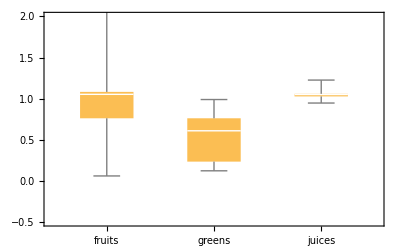

```mathematica
BoxWhiskerChart[den,PlotRange->{-.5,2},ChartLabels->{"fruits","greens","juices"}]
```

It looks like greens tend to be much less dense, but what is the fruit with the ridiculous density?  Here are the outlying fruit items, which have a density greater than that of lead. Maybe it’s the pasta making it dense.

```mathematica
Select[den[[1]],#>Entity["Element","Lead"][EntityProperty["Element","Density"]]&]
```

<|PREGO Pasta, Chunky Garden Tomato, Onion and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3,PREGO Pasta, Tomato, Basil and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3|>

## Fruit Color Space

I decided to investigate the colors of smoothies one could make from different kinds of ingredients.

```mathematica
insideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalInsideColors"]
SetAttributes[insideColorsetOfFoodType,Listable]
```

```mathematica
outsideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalOutsideColors"]
SetAttributes[outsideColorsetOfFoodType,Listable]
```

```mathematica
rgbFromColorset[set_]:=EntityValue[set,EntityProperty["ColorSet","TypicalColorValue"]]
```

Apples have certain exterior colors given as names:

```mathematica
outsideColorsetOfFoodType[]
```

{brown,cream,green,red,white,yellow}

We get instances of these colors.

```mathematica
rgbFromColorset@%
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Note that we can also see their interior colors, which aren’t quite as pretty.

```mathematica
rgbFromColorset@insideColorsetOfFoodType[]
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Generate a 3D span of the exterior in XYZ color space and display it in 3D color space:

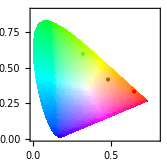

```mathematica
ChromaticityPlot[rgbFromColorset[outsideColorsetOfFoodType[]]]
```

Define functions to generate instances of possible fruit colors based on its exterior colors .

```mathematica
fruitColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[outsideColorsetOfFoodType[fruit]],"XYZ"]
fruitInsideColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[insideColorsetOfFoodType[fruit]],"XYZ"]
fruitColorHull[fruit_]:=ConvexHullMesh[fruitColorList[fruit]]
```

Here we generate a lot of possible apple colors by picking random points within the color space.

```mathematica
applecolors=XYZColor@@@RandomPoint[fruitColorHull[],100]
```

{XYZColor[0.7138540391558005, 0.8192063543438001, 0.5088632531028084],XYZColor[0.5163907306996992, 0.770421122918843, 0.12307336519666257],XYZColor[0.664850829533587, 0.638660291723076, 0.2024727537996065],XYZColor[0.5353832519744212, 0.5834155905247934, 0.3521639751833766],XYZColor[0.569233784091684, 0.7027533620592515, 0.14671758937883816],XYZColor[0.4275303212500555, 0.6740475907195279, 0.13822912404548537],XYZColor[0.8513783806455725, 0.9286467154503569, 0.4070559061606923],XYZColor[0.7245847212309221, 0.8468754111621067, 0.3250185706889622],XYZColor[0.4158856107467418, 0.4178694074484418, 0.22536207320405277],XYZColor[0.4991677528277493, 0.6982634303194987, 0.09741532489039295],XYZColor[0.29295410461391136, 0.26944020152561776, 0.12437326316739894],XYZColor[0.35107929127147064, 0.3853332403437054, 0.12970220429637958],XYZColor[0.6904957516353348, 0.6684089439807334, 0.44850967837261024],XYZColor[0.6246005836721901, 0.7452023084499592, 0.15998479254363085],XYZColor[0.4128774826334106, 0.6633873931633681, 0.1240539533114614],XYZColor[0.46336574665468866, 0.6394470930001154, 0.11387261567917539],XYZColor[0.4840786523262076, 0.3768671539007832, 0.1916751469973197],XYZColor[0.6801323496619157, 0.7554037597494329, 0.49518287920809734],XYZColor[0.5023765049280077, 0.6591913180753314, 0.10107187240041038],XYZColor[0.8883712023562537, 0.9557823339523385, 0.6446129043586329],XYZColor[0.5991521645684802, 0.5531136438285899, 0.08923990148189465],XYZColor[0.7069698317959187, 0.7827631520758122, 0.32183689100141966],XYZColor[0.4206419471281855, 0.42972624184841723, 0.1335121022024669],XYZColor[0.7160575302669577, 0.8183120047895004, 0.5309946215739206],XYZColor[0.5942868819656345, 0.6785681487688741, 0.29722870802075885],XYZColor[0.6122367228158666, 0.739950886409957, 0.3428797371400817],XYZColor[0.6408697551216661, 0.6315205303241443, 0.12953125038682722],XYZColor[0.8774240563985106, 0.935791191625949, 0.5351722973139047],XYZColor[0.6632402313926392, 0.7049938974873712, 0.4492163000727273],XYZColor[0.5947256409406759, 0.7947833216671717, 0.13758624556289423],XYZColor[0.5587244244469164, 0.6241861887774595, 0.08965592664782218],XYZColor[0.4868186265607676, 0.5199610239755231, 0.1506637383449605],XYZColor[0.6611067814696997, 0.6764387524127703, 0.46490141275340513],XYZColor[0.3501231727068598, 0.41005711813194223, 0.1454804795583633],XYZColor[0.2229065531880804, 0.2116726212902743, 0.0464332616055545],XYZColor[0.5772519883207295, 0.5680045130024517, 0.13830077779442662],XYZColor[0.830933145704574, 0.8226172968884712, 0.5849376625024104],XYZColor[0.4238509944008487, 0.7128660610100283, 0.11594710417863863],XYZColor[0.7495397272281675, 0.8327381988942358, 0.40978168605262655],XYZColor[0.4235376390006822, 0.4496768728964572, 0.206025917046483],XYZColor[0.43085021577021554, 0.45264243443272456, 0.08363652310346392],XYZColor[0.41013602841742924, 0.4100590920649293, 0.1216586592001111],XYZColor[0.51531630211018, 0.655600987917777, 0.22521009745764198],XYZColor[0.537235744247116, 0.7077343600922491, 0.17344060192098054],XYZColor[0.6853198768553087, 0.8323471880595273, 0.18108649209596783],XYZColor[0.7128715567494696, 0.8119729014404108, 0.2730385211306673],XYZColor[0.5984801275592816, 0.681183575078376, 0.1096938194239091],XYZColor[0.5888127431090197, 0.6122401952042263, 0.32601047330861277],XYZColor[0.6024644914252689, 0.5904042246451272, 0.2746372766431705],XYZColor[0.7598807258827275, 0.8208327088022173, 0.3235224606356758],XYZColor[0.49921408172720494, 0.5272518351239482, 0.08830780327236742],XYZColor[0.5862272681816626, 0.4958077940289579, 0.08933951415438912],XYZColor[0.8499923111526987, 0.9217297926475007, 0.42871401530966746],XYZColor[0.5285501933188662, 0.4577079083543, 0.10154189669382963],XYZColor[0.701340300572543, 0.7700376758779018, 0.204412059810389],XYZColor[0.7836519887907215, 0.8877241566016499, 0.4238818508729335],XYZColor[0.5841807134193139, 0.7237076480677397, 0.2716936838485361],XYZColor[0.302865806098935, 0.35663794236102564, 0.09521273355039273],XYZColor[0.590767754807236, 0.8084228173408688, 0.14564067996830332],XYZColor[0.5069310604160703, 0.7327908558041872, 0.24228064692964002],XYZColor[0.4953348960338647, 0.7234230763907744, 0.1640906382103675],XYZColor[0.5417247560167481, 0.6744636254411608, 0.2903140268156622],XYZColor[0.6592298616267073, 0.7576358559277508, 0.18118834586496235],XYZColor[0.4932401674756709, 0.5894094384669529, 0.14424236534418633],XYZColor[0.7178062910544601, 0.7958310119939288, 0.37838972936908355],XYZColor[0.6188496690803013, 0.5507918484135682, 0.2675186681367555],XYZColor[0.5342047888309202, 0.7783080470789675, 0.2576466327098349],XYZColor[0.518357846920794, 0.662896267238498, 0.27969168050526527],XYZColor[0.7323642284765438, 0.8414631679758734, 0.27772856795464873],XYZColor[0.6133257055994473, 0.6465005573043648, 0.37962345315400603],XYZColor[0.28239209010825084, 0.3884929454795095, 0.06489441933100804],XYZColor[0.5476804831180787, 0.4713429081329136, 0.09382270074102672],XYZColor[0.8472368518701655, 0.9299341874419466, 0.5481373945560969],XYZColor[0.746787721379916, 0.71566491795855, 0.5119561970921492],XYZColor[0.7808519855279216, 0.8709101766332327, 0.17322640616423657],XYZColor[0.7158308934176941, 0.8621487635321573, 0.3309960541004785],XYZColor[0.6008730568529709, 0.6773486360783124, 0.14477351113983516],XYZColor[0.5181107068412499, 0.7522829094492195, 0.19552131048084465],XYZColor[0.6373412531789121, 0.8121725908256104, 0.28902531796053677],XYZColor[0.5813983167786557, 0.5532207331616509, 0.2060889542496117],XYZColor[0.6254488607848084, 0.6816379371230749, 0.3377884214576229],XYZColor[0.7960673461401623, 0.8475738233351141, 0.30997323230356477],XYZColor[0.7181431705445759, 0.7200409588566522, 0.5438775246910158],XYZColor[0.6773845296973341, 0.7917314869235269, 0.3269111171337752],XYZColor[0.8473440147606234, 0.9409248486500105, 0.5797319716018862],XYZColor[0.5679546106724515, 0.6550374857720024, 0.32575424442191714],XYZColor[0.7022749831494292, 0.6252070607682544, 0.3926387884099022],XYZColor[0.5968844220993726, 0.7890627639053772, 0.3400108965869387],XYZColor[0.6882944316615195, 0.7446693481359429, 0.39342941774432416],XYZColor[0.5132214322249552, 0.5047369744105038, 0.3293303918905325],XYZColor[0.4881754054290576, 0.5350429500771129, 0.23702899436775515],XYZColor[0.7231713673499286, 0.7724498644971459, 0.1931821949374185],XYZColor[0.5398602451668738, 0.6837811036145086, 0.284611140085003],XYZColor[0.4436395304826152, 0.48743428921873344, 0.07826142348661325],XYZColor[0.5289575311792073, 0.4461261251916132, 0.1340325110180809],XYZColor[0.5544598003255384, 0.636494334123907, 0.15306596906997927],XYZColor[0.6360657367674417, 0.8132393284535021, 0.30684982947740214],XYZColor[0.3917804442511047, 0.6011028566116495, 0.14780191305217016],XYZColor[0.5226520041138317, 0.5950401272497784, 0.15989261722617243],XYZColor[0.8129531219053906, 0.8840890585952995, 0.32615510703003536]}

And visualize them in 3D and 2D space:

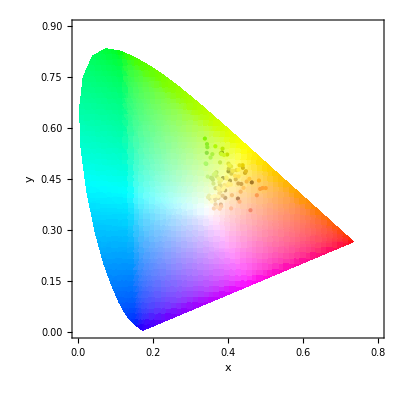
-Graphics3D-
-Graphics-

```mathematica
{ChromaticityPlot3D[#],ChromaticityPlot[#]}&[applecolors]//TableForm
```

To visualize the possible colors in a combination of fruits, we combine the color lists of our fruits of interest.

```mathematica
cols=fruitColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.5705847727555028, 0.5939107140662322, 0.4962367058369933],XYZColor[0.7675311107867991, 0.7514084589678663, 0.527898801477504],XYZColor[0.8631237862613351, 0.9255207554907926, 0.543050771361307],XYZColor[0.4750293186617195, 0.5100949684019024, 0.4921147299829064],XYZColor[0.38762245843099563, 0.24999598168665826, 0.2643667247495506],XYZColor[0.3175964667912231, 0.33722303380133345, 0.2083536190467722],XYZColor[0.7674537424025288, 0.8763126149708859, 0.524527540616286],XYZColor[0.36719343149518957, 0.30584032763482394, 0.06274653335429636],XYZColor[0.6019834874037967, 0.5886458122458073, 0.5656664081002701],XYZColor[0.34044283050447943, 0.46822845021156, 0.060834888052052505],XYZColor[0.4194475311566218, 0.5198224047307548, 0.17410191346168002],XYZColor[0.651781438686256, 0.5691331196590764, 0.35769805132920085],XYZColor[0.3787737291983385, 0.42682061483353484, 0.3581561756995769],XYZColor[0.6417685684281066, 0.6499025467206533, 0.13670683267334904],XYZColor[0.7217884991590934, 0.8056378500715159, 0.2508323966276996],XYZColor[0.2937270010483294, 0.2838603750220995, 0.059678333274790996],XYZColor[0.5548717985134072, 0.525406705739868, 0.6717221623379747],XYZColor[0.217322863226047, 0.2807175674739314, 0.3871131816675536],XYZColor[0.16396871415637737, 0.11965533089616909, 0.5634278950852086],XYZColor[0.5903205495511451, 0.5872687063489225, 0.5310021034209215],XYZColor[0.386969870910708, 0.3518926245482542, 0.5082052088946954],XYZColor[0.3676029056758304, 0.2872572073218843, 0.2497512981236053],XYZColor[0.34077649123616294, 0.38396555000532195, 0.5355522227423645],XYZColor[0.5764898190168958, 0.5830815744316947, 0.4835673363063001],XYZColor[0.5181330005611472, 0.5023149907477321, 0.5564328418077106],XYZColor[0.3031653827479944, 0.20168082945897925, 0.41835789499579723],XYZColor[0.22312350715933194, 0.12323328236617381, 0.35529963153247224],XYZColor[0.3066419807457129, 0.3352904965149862, 0.08154146849567012],XYZColor[0.6796765952465064, 0.6376459148420418, 0.43368456835766567],XYZColor[0.3297969937221156, 0.39635068698646625, 0.264854616439384],XYZColor[0.4219801197518419, 0.6530177699076968, 0.16077291730854215],XYZColor[0.39258990370880753, 0.617219534916927, 0.21718376309586207],XYZColor[0.45727719150540935, 0.33283562580246906, 0.2022400738054947],XYZColor[0.7639738515911413, 0.8870615465573727, 0.31310218019003033],XYZColor[0.503248868027459, 0.5395894569406804, 0.33911818467472965],XYZColor[0.2297817609577698, 0.3156006797025833, 0.22969145272794023],XYZColor[0.5301199198103478, 0.48185430321363054, 0.23345878683310517],XYZColor[0.3278013398564358, 0.3196716469200872, 0.4550000726275786],XYZColor[0.6484816978951299, 0.6199676943912585, 0.16259254944048196],XYZColor[0.5775157921293449, 0.604947558572191, 0.08649409102568828],XYZColor[0.21545065855782985, 0.22316084339240694, 0.5789143158262043],XYZColor[0.5009046616804419, 0.4992473689584179, 0.05992423325465723],XYZColor[0.7108980101181676, 0.8338798311684569, 0.535068291611173],XYZColor[0.6283049988575135, 0.7163690573389131, 0.5454496206602034],XYZColor[0.4758845241265336, 0.44041119493872627, 0.10036713636842953],XYZColor[0.772737057173626, 0.90795663029454, 0.4161618593416706],XYZColor[0.3602186880499961, 0.6013262161729772, 0.12941445065923685],XYZColor[0.37869830439270735, 0.3551755083401572, 0.3928409789502795],XYZColor[0.586979658145092, 0.6565168509629628, 0.44395656529043814],XYZColor[0.33513000557016637, 0.35875563006473576, 0.04695090541928559],XYZColor[0.46654075936264194, 0.5844483500086962, 0.3336153349981891],XYZColor[0.2587371564066224, 0.45429930726076273, 0.12483898295163653],XYZColor[0.42622934409470903, 0.515593187397909, 0.5276616101943791],XYZColor[0.2308588700243256, 0.19251586494991024, 0.4887813689564299],XYZColor[0.29857106434764324, 0.30716067434515504, 0.19846111968118374],XYZColor[0.5850880529925252, 0.5735314050878072, 0.6351858461159624],XYZColor[0.5252060369864023, 0.3661858535737673, 0.11934429714053185],XYZColor[0.41941284690517733, 0.5643896222112516, 0.3267588628216108],XYZColor[0.16532511164325314, 0.13395393056499205, 0.1885753355649621],XYZColor[0.2895690260221292, 0.17300852760296992, 0.3487722312474676],XYZColor[0.3028209638210656, 0.4993071094938869, 0.20157439919100362],XYZColor[0.5669566440161516, 0.4785557683427847, 0.2580945176361621],XYZColor[0.23403345774884976, 0.3345483613233967, 0.27004731714663965],XYZColor[0.6305001645496587, 0.729947081339121, 0.5384359257322141],XYZColor[0.21448377237132232, 0.12643319492534266, 0.4320647612261813],XYZColor[0.4149938329186368, 0.32955705484625153, 0.47313227746589515],XYZColor[0.6094898831214824, 0.6513659480913788, 0.6052801644990066],XYZColor[0.39835646026190064, 0.7063254350746807, 0.1316600883503296],XYZColor[0.31047093567514994, 0.4162966969377745, 0.41065443565435167],XYZColor[0.7534690170285049, 0.7238983753726375, 0.5453595015967202],XYZColor[0.4080258840929588, 0.5780440830235595, 0.31909460215463137],XYZColor[0.5291998635433114, 0.604674492874835, 0.10079798744933743],XYZColor[0.3448270441071063, 0.4388545260942992, 0.44792873507222575],XYZColor[0.6139806732634417, 0.7882968936768647, 0.45255331267039567],XYZColor[0.489657174914074, 0.5583813251893649, 0.5649979152379033],XYZColor[0.5559597905602086, 0.7169377753929197, 0.13193768351909263],XYZColor[0.37241320552598267, 0.4305768497386405, 0.08742632420091212],XYZColor[0.3266995298443828, 0.33122160420769775, 0.5635155698763407],XYZColor[0.5116667987295828, 0.7644383592871277, 0.17827034887064375],XYZColor[0.3308059558346187, 0.37919959734769637, 0.5317299539513985],XYZColor[0.35729242400596684, 0.28404101022590245, 0.39385090630102415],XYZColor[0.6393117016294622, 0.630774880186857, 0.2224328714740028],XYZColor[0.16437606156496865, 0.26875285814218264, 0.11921410573856361],XYZColor[0.7495718937607493, 0.8897126066193065, 0.3297209530221118],XYZColor[0.48438009336148913, 0.4467555090018597, 0.7208623134197248],XYZColor[0.5788846484018307, 0.52817710731478, 0.5231771897091878],XYZColor[0.39197441279291734, 0.48739024573020184, 0.36002340570077707],XYZColor[0.4911775967032025, 0.42749645189064067, 0.48275180869570267],XYZColor[0.12779823298462445, 0.17081432456643697, 0.1855315866306836],XYZColor[0.5864471563221422, 0.6064651715597152, 0.21086300109386136],XYZColor[0.6976840332687656, 0.6935310518383978, 0.36001928454388377],XYZColor[0.5332588638052399, 0.43220098828460507, 0.3205841009318925],XYZColor[0.26290583735682194, 0.29976534183975045, 0.18675823584891404],XYZColor[0.2718381496177381, 0.19449165870082175, 0.489151124920978],XYZColor[0.6546889134676145, 0.6880970817905186, 0.5027790112511038],XYZColor[0.20019578990753006, 0.34808769385494676, 0.07911633695439002],XYZColor[0.6001520557127434, 0.6095620699482697, 0.3327316556762764],XYZColor[0.6038819506388865, 0.5900906760311392, 0.4594184232285382],XYZColor[0.6787517941290188, 0.7935657366524661, 0.1647201642963757],XYZColor[0.6378179701440748, 0.7855311362331293, 0.4457590542378035]}

Mixtures of pure fruit colors spans a good deal of space. However, this is based on the generic color names and doesn’t take into account the likely muted actual values.

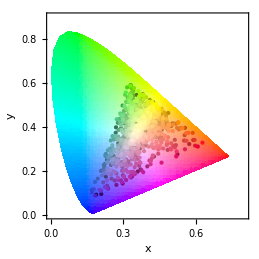

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],1000]]
```

We can try doing the same with interior colors. I’m using Interpreter to get the entities for the string inputs.

```mathematica
innerColors=fruitInsideColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.41558995549450517, 0.37915036103760824, 0.3504173124197042],XYZColor[0.4833716653173311, 0.49845038002585407, 0.4038408701401871],XYZColor[0.7730590831094583, 0.8615143733467451, 0.1323934452499057],XYZColor[0.193354384557212, 0.09746421943330363, 0.15286671637260596],XYZColor[0.23347649915426538, 0.15022909797618078, 0.20365879719029956],XYZColor[0.18344796137112473, 0.09541819342600666, 0.6685001094006081],XYZColor[0.21858541921983965, 0.13351220327710867, 0.5357034539298752],XYZColor[0.3932322421891562, 0.3560883659318884, 0.15035138968537864],XYZColor[0.207180082181201, 0.138521121792896, 0.4316613604938152],XYZColor[0.6272143306158734, 0.6220410307259002, 0.551530436689755],XYZColor[0.4740609432192483, 0.4391245476181692, 0.05106256354191785],XYZColor[0.31628528119910093, 0.16141028525479462, 0.2253239139409705],XYZColor[0.6834109231607818, 0.6569365812821478, 0.37920698013501075],XYZColor[0.561245246465503, 0.4481847020095343, 0.13011828382988222],XYZColor[0.6611614839325765, 0.6731797626576116, 0.253796629144745],XYZColor[0.37617135015030445, 0.34900281524068444, 0.43210024665380764],XYZColor[0.4054280499033748, 0.32553331516922934, 0.16689315332596177],XYZColor[0.1488258305856519, 0.09636671925583074, 0.1540258129209836],XYZColor[0.5753796462329389, 0.508862053731148, 0.29187824926932093],XYZColor[0.2785594609554968, 0.1747236829102502, 0.2357238233329194],XYZColor[0.43511408606885815, 0.35189259910337534, 0.44216873667626466],XYZColor[0.5642942244916606, 0.5426018940343905, 0.15338120972632185],XYZColor[0.3718841570374577, 0.22588593608724927, 0.3307010200296806],XYZColor[0.11875343878189126, 0.06003278516780275, 0.15593143790794772],XYZColor[0.4256936466796756, 0.3378612453780624, 0.23829190484734897],XYZColor[0.5512917739231752, 0.5821761428195643, 0.06784875671740287],XYZColor[0.5786162828515206, 0.539467079684487, 0.15477364041659392],XYZColor[0.6380033462659488, 0.6693228252019637, 0.40587092878487285],XYZColor[0.6984520563339703, 0.6921029946869172, 0.14695472165062406],XYZColor[0.47240663801951965, 0.36848295342225923, 0.14219033211330656],XYZColor[0.45696467439525057, 0.47285870375803307, 0.16491343501952171],XYZColor[0.4214280346667959, 0.2744999258538302, 0.2408796525022704],XYZColor[0.7354631182185377, 0.7540534338866564, 0.6454707198585042],XYZColor[0.14215895740701423, 0.07428236499339536, 0.3442651638448594],XYZColor[0.6414424743581669, 0.6709092575374694, 0.12966206391472623],XYZColor[0.540428087084632, 0.5229390765371634, 0.2398164605048253],XYZColor[0.2673716312284483, 0.19405999646986094, 0.3643490640564738],XYZColor[0.21244498425711, 0.181732550188079, 0.1479631834535693],XYZColor[0.044643505982729814, 0.045525260099526066, 0.03817599902132984],XYZColor[0.7205103402852656, 0.766439874250414, 0.4177955062598976],XYZColor[0.7704045687517668, 0.7662640563587039, 0.5642183631387575],XYZColor[0.6029127704112806, 0.5902590094127372, 0.6744516946978397],XYZColor[0.48680022559354763, 0.43264755236478625, 0.5363141758214972],XYZColor[0.4105276329416888, 0.374925385762617, 0.12132120407331881],XYZColor[0.7821448639771379, 0.828685143089359, 0.4386543837533813],XYZColor[0.5880741126362837, 0.563178303711734, 0.72687078543689],XYZColor[0.4208248329989407, 0.38149665964863055, 0.12639274082147722],XYZColor[0.3468527433010554, 0.32345611783741723, 0.3657105388935905],XYZColor[0.5567644778095459, 0.5335089162872876, 0.3134889317551436],XYZColor[0.26611093769585203, 0.28110599251614643, 0.1077936255791685],XYZColor[0.7892736041617089, 0.8599914812690371, 0.3591431563697641],XYZColor[0.46268440142397493, 0.41646896760827234, 0.20366703439067446],XYZColor[0.5195161565415761, 0.41996508143892675, 0.43837244553076704],XYZColor[0.8207592890350816, 0.9117596188842979, 0.2110537850119948],XYZColor[0.7640902398830777, 0.8310496912384177, 0.10408690410481469],XYZColor[0.42520409909210877, 0.35567316968368823, 0.4755728238903413],XYZColor[0.2575038002939011, 0.16697735984604412, 0.49988221377561326],XYZColor[0.373588012691645, 0.3901679878884433, 0.1508296021298945],XYZColor[0.6585285730487457, 0.7252738961197779, 0.14471872803395203],XYZColor[0.7775300748034232, 0.8225208169142958, 0.4520668200780732],XYZColor[0.8119808062475246, 0.8435017287986167, 0.5004470050419564],XYZColor[0.8744435061216637, 0.910127469472186, 0.5737600065206082],XYZColor[0.7415163130758934, 0.7343484512119579, 0.7058079837827739],XYZColor[0.4316964173879515, 0.3966928712445442, 0.6861942915682114],XYZColor[0.35709347425978655, 0.3277182550887613, 0.341965090219026],XYZColor[0.5164296159782144, 0.5115005693150195, 0.4861496649183771],XYZColor[0.5099355432713514, 0.515224961597834, 0.1671157449721481],XYZColor[0.7625900590727791, 0.7577786662272413, 0.6397685289439242],XYZColor[0.50369603682134, 0.41302699753012184, 0.144171407069276],XYZColor[0.6187126920130833, 0.5125229365620115, 0.34189284673289533],XYZColor[0.4079192676464446, 0.4379214869365998, 0.1288945160112004],XYZColor[0.4020093646779114, 0.2951473635547949, 0.4301027595304213],XYZColor[0.49515040700829804, 0.4378772844980515, 0.12720465691666438],XYZColor[0.5417599547872848, 0.5009762117653372, 0.6563984405074564],XYZColor[0.4416531436371386, 0.471983072425496, 0.14810173838639273],XYZColor[0.5203101726504474, 0.45733049295258554, 0.3483205710264584],XYZColor[0.3038599422239717, 0.2136956197043084, 0.23006824444298923],XYZColor[0.64393467043345, 0.6607204002108938, 0.18461707187077903],XYZColor[0.19862502219907918, 0.1380108858547774, 0.09952338946255745],XYZColor[0.5846029444187192, 0.5602260964044022, 0.17531944977898217],XYZColor[0.2457443262582858, 0.17935778945604863, 0.5993000476254259],XYZColor[0.14101211084445098, 0.13389876896256825, 0.08769309477899456],XYZColor[0.627574377481425, 0.6023369038687273, 0.18220449501748404],XYZColor[0.48843138977162515, 0.3064898456486672, 0.07574135456536812],XYZColor[0.48164684822305237, 0.4541460897806907, 0.7130647376380571],XYZColor[0.8187083955860702, 0.8602994564881185, 0.3976086154089965],XYZColor[0.3697899571896225, 0.23854675905273182, 0.26404037938724734],XYZColor[0.2838404957891564, 0.1963535949082157, 0.5120523327249921],XYZColor[0.25272872241806177, 0.18484761639966496, 0.36371645068618574],XYZColor[0.6732020250511282, 0.6786074500225024, 0.45192936536692174],XYZColor[0.08959027555386923, 0.053070146847444266, 0.16173533100774395],XYZColor[0.5512855749147619, 0.524832221652782, 0.7132926769643394],XYZColor[0.6982397841090505, 0.769801276675219, 0.1733572126931362],XYZColor[0.40395543916101173, 0.3658449850126625, 0.18403142981913334],XYZColor[0.33746886060419967, 0.3781357065280472, 0.07663535731033932],XYZColor[0.7081571772592136, 0.7132002311713822, 0.49686488670738516],XYZColor[0.2456980614024299, 0.2500175817043212, 0.10442303603082603],XYZColor[0.6420790687597221, 0.5922686991336678, 0.11284574992993135],XYZColor[0.5902977648337969, 0.6021422478962036, 0.24089049933472018],XYZColor[0.8725749533717616, 0.9026470321016177, 0.5787956414332781]}

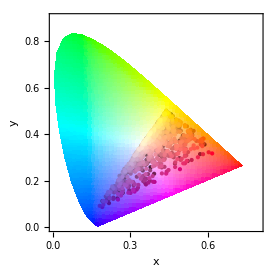

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[innerColors,1]],1000]]
```

The inside colors cover much less of the greens.

Let’s fill some fruitbowls with these fruits.

#### Salad bowl

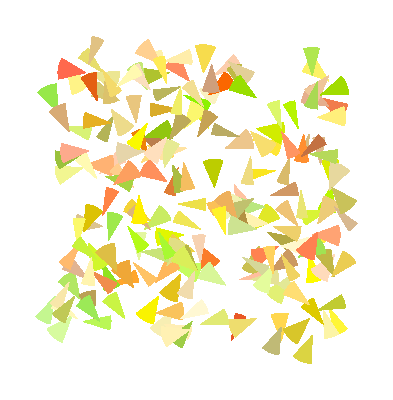

```mathematica
appleImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/8,Pi/4}]}]},200]]
```

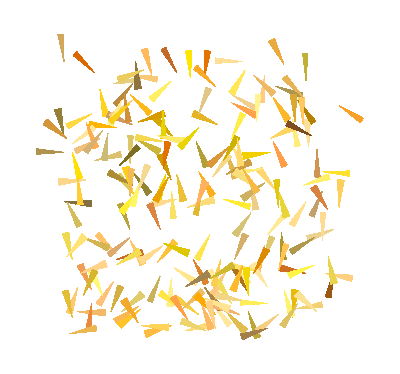

```mathematica
carrotImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/16,Pi/12}]}]},200]]
```

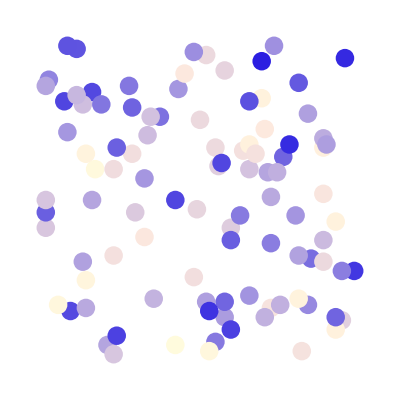

```mathematica
berryImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,0.3]},100]]
```

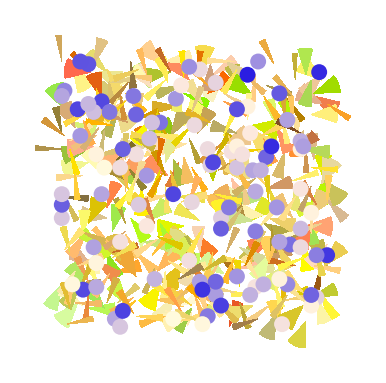

```mathematica
Show[appleImage,carrotImage,berryImage]
```

This concludes our stroll through food data.